```mathematica
f1[x_]:= Sin[2x] -  Sin[x/4] - Sin[x/8]
```

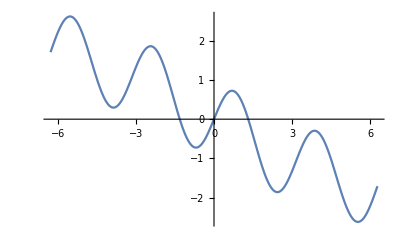

```mathematica
Plot[f1[x], {x, -2Pi, 2Pi}]
```

```mathematica
f2[x_, y_] := Cos[x] + f1[y]/2
```

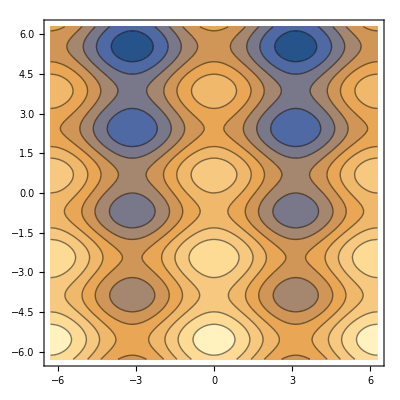

```mathematica
ContourPlot[f2[x,y], {x, -2Pi, 2Pi}, {y, -2Pi, 2Pi}]
```

```mathematica
(*ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]*)
ContourPlot3D[f2[x,y]+z, {x, 0, 2Pi}, {y, 0, 2Pi}, {z, 0, 1}]
```

-Graphics3D-

ContourPlot3d really needs 3 variables (x, y, z), so I added a third value to the f2 function.

```mathematica
And now just trying some formatting. (Code)
Some more styles. (Subsection)
- item number 1
- subitem
- item paragraph (whatever that means)
```